```mathematica
f[x_,y_]=(x^2+y^2-2 x)^2-24*(x^2+y^2)
```

-24 (x^2+y^2)+(-2 x+x^2+y^2)^2

```mathematica
g[x_,y_]=Sin[2 x+y]-4 y - 3x+2
```

2-3 x-4 y+Sin[2 x+y]

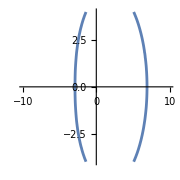

```mathematica
gr1=ContourPlot[f[x,y]==0,{x,-10,10},{y,-4,4},Axes->True,Frame->False,ImageSize->Small]
```

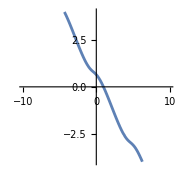

```mathematica
gr2=ContourPlot[g[x,y]==0,{x,-10,10},{y,-4,4},Axes->True,Frame->False,ImageSize->Small]
```

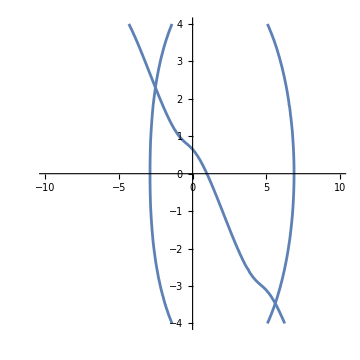

```mathematica
Show[gr1,gr2,ImageSize->Medium]
```

```mathematica
FindRoot[{f[x,y]==0,g[x,y]==0},{x,-3},{y,2}]
```

{x→-2.52894,y→2.30253}

```mathematica
FindRoot[{f[x,y]==0,g[x,y]==0},{x,5},{y,-3}]
```

{x→5.61885,y→-3.46496}